```mathematica
SetDirectory[NotebookDirectory[]<>"RGBeta"];
<<RGBeta`
```

The package RGBeta` is already loaded. Please restart the kernel to reload it.

## Initial Conditions

```mathematica
GeV=1;
TeV=10^3 GeV;
mZ=91.1876 GeV; 
alpha1t=0.010277175555560035(*.016830*);
alpha2t=0.033368505145062(*.03347*);
alpha3t=0.1083014023511993(*.1184*);
```

```mathematica
v=246.2GeV;
yTopMS=0.93558;
mtMS=yTopMS*v/Sqrt[2]; 
yTopMS=mtMS*Sqrt[2]/v;
lambda1mtMS= .12710; 
mHphys=Sqrt[2*lambda1mtMS] v GeV; 
mPl=1.2*10^19GeV;
```

```mathematica
vlqmass=2TeV;
vlqyuk=1;
higgsmassparam=-mHphys^2/2;
mH=15TeV;
ΛNP=1000TeV;
```

## Run up to VLQ mass (m^2<0)

```mathematica
ResetModel[]
```

```mathematica
AddGaugeGroup[g1,U1Y,U1]
AddGaugeGroup[g2,SU2L,SU[2]]
AddGaugeGroup[g3,SU3c, SU[3]]
Dim[gen]=ng;
AddFermion[q,GaugeRep->{U1Y[1/6],SU2L[fund],SU3c[fund]},FlavorIndices->{gen}]
AddFermion[u,GaugeRep->{U1Y[-2/3],Bar@SU3c[fund]},FlavorIndices->{gen}]
AddFermion[d,GaugeRep->{U1Y[1/3],Bar@SU3c[fund]},FlavorIndices->{gen}]
AddFermion[l,GaugeRep->{U1Y[-1/2],SU2L[fund]},FlavorIndices->{gen}]
AddFermion[e,GaugeRep->{U1Y[1]},FlavorIndices->{gen}]
AddScalar[H,GaugeRep->{U1Y[1/2],SU2L[fund]}]
AddYukawa[yu,{H,q,u},
GroupInvariant->(del[SU3c@fund,#2,#3]eps[SU2L@fund,#2,#1]&),
CouplingIndices->({gen[#2],gen[#3]}&),
Chirality->Right]
AddYukawa[yd,{Bar@H,q,d},
GroupInvariant->(del[SU3c@fund,#2,#3]del[SU2L@fund,#1,#2]&),
CouplingIndices->({gen[#2],gen[#3]}&),
Chirality->Right]
AddYukawa[ye,{Bar@H,l,e},
GroupInvariant->(del[SU2L@fund,#1,#2]&),
CouplingIndices->({gen[#2],gen[#3]}&),
Chirality->Right]
AddQuartic[λ1,{Bar@H,H,Bar@H,H},
GroupInvariant->((del[SU2L@fund,#1,#2]del[SU2L@fund,#3,#4])&)]
AddScalarMass[μ2,{Bar@H,H},
GroupInvariant->(del[SU2L@fund,#1,#2]&)]
Keys@$couplings
CheckProjection/@%
```

{g1,g2,g3,yu,yd,ye,λ1,μ2}

{g1^2,g2^2,g3^2,yu_($i,$j),yd_($i,$j),ye_($i,$j),λ1,μ2}

```mathematica
matrixSubs={yu->DiagonalMatrix@{0,0,yt},
yd->DiagonalMatrix@{0,0,0},
ye->DiagonalMatrix@{0,0,0},
ng->3};
SetReal[yc,yt,yb,yτ]
```

```mathematica
replacementListSM={yt->Sqrt[4*Pi*αtSM[t]],g1->Sqrt[4*Pi*α1SM[t]],g2->Sqrt[4*Pi*α2SM[t]],g3->Sqrt[4*Pi*α3SM[t]],μ2->μ2SM[t],λ1->λ1SM[t]}
```

{yt→2 √π √αtSM[t],g1→2 √π √α1SM[t],g2→2 √π √α2SM[t],g3→2 √π √α3SM[t],μ2→μ2SM[t],λ1→λ1SM[t]}

```mathematica
eqn1SM=α1SM'[t]==(Expand[Finalize[BetaFunction[g1,2],Parameterizations->matrixSubs]]/(4*Pi))/.replacementListSM
eqn2SM=α2SM'[t]==(Expand[Finalize[BetaFunction[g2,2],Parameterizations->matrixSubs]]/(4*Pi))/.replacementListSM
eqn3SM=α3SM'[t]==(Expand[Finalize[BetaFunction[g3,2],Parameterizations->matrixSubs]]/(4*Pi))/.replacementListSM
eqn4SM=
λ1SM'[t]==(Expand[Finalize[BetaFunction[λ1,2],Parameterizations->matrixSubs]]/.replacementListSM)
eqn5SM=
μ2SM'[t]==(Expand[Finalize[BetaFunction[μ2,2],Parameterizations->matrixSubs]]/.replacementListSM)
eqn6SM=αtSM'[t]==(Expand[Finalize[BetaFunction[yu,2],Parameterizations->matrixSubs][[3,3]]*(yt/(2*Pi))/.replacementListSM])
```

α1SM'[t]==1/(4 π)((41 α1SM[t]^2)/3+(199 α1SM[t]^3)/(36 π)+(9 α1SM[t]^2 α2SM[t])/(4 π)+(22 α1SM[t]^2 α3SM[t])/(3 π)-(17 α1SM[t]^2 αtSM[t])/(12 π))

α2SM'[t]==(-19/3 α2SM[t]^2+(3 α1SM[t] α2SM[t]^2)/(4 π)+(35 α2SM[t]^3)/(12 π)+(6 α2SM[t]^2 α3SM[t])/π-(3 α2SM[t]^2 αtSM[t])/(4 π))/(4 π)

α3SM'[t]==(-14 α3SM[t]^2+(11 α1SM[t] α3SM[t]^2)/(12 π)+(9 α2SM[t] α3SM[t]^2)/(4 π)-(13 α3SM[t]^3)/π-(α3SM[t]^2 αtSM[t])/π)/(4 π)

λ1SM'[t]==(3 α1SM[t]^2)/8-(379 α1SM[t]^3)/(192 π)+3/4 α1SM[t] α2SM[t]-(559 α1SM[t]^2 α2SM[t])/(192 π)+(9 α2SM[t]^2)/8-(289 α1SM[t] α2SM[t]^2)/(192 π)+(305 α2SM[t]^3)/(64 π)-(19 α1SM[t]^2 αtSM[t])/(16 π)+(21 α1SM[t] α2SM[t] αtSM[t])/(8 π)-(9 α2SM[t]^2 αtSM[t])/(16 π)-6 αtSM[t]^2-(2 α1SM[t] αtSM[t]^2)/(3 π)-(8 α3SM[t] αtSM[t]^2)/π+(15 αtSM[t]^3)/(2 π)-(3 α1SM[t] λ1SM[t])/(4 π)+(629 α1SM[t]^2 λ1SM[t])/(384 π^2)-(9 α2SM[t] λ1SM[t])/(4 π)+(39 α1SM[t] α2SM[t] λ1SM[t])/(64 π^2)-(73 α2SM[t]^2 λ1SM[t])/(128 π^2)+(3 αtSM[t] λ1SM[t])/π+(85 α1SM[t] αtSM[t] λ1SM[t])/(96 π^2)+(45 α2SM[t] αtSM[t] λ1SM[t])/(32 π^2)+(5 α3SM[t] αtSM[t] λ1SM[t])/π^2-(3 αtSM[t]^2 λ1SM[t])/(16 π^2)+(3 λ1SM[t]^2)/(2 π^2)+(9 α1SM[t] λ1SM[t]^2)/(16 π^3)+(27 α2SM[t] λ1SM[t]^2)/(16 π^3)-(9 αtSM[t] λ1SM[t]^2)/(4 π^3)-(39 λ1SM[t]^3)/(32 π^4)

μ2SM'[t]==-(3 α1SM[t] μ2SM[t])/(8 π)+(557 α1SM[t]^2 μ2SM[t])/(768 π^2)-(9 α2SM[t] μ2SM[t])/(8 π)+(15 α1SM[t] α2SM[t] μ2SM[t])/(128 π^2)-(145 α2SM[t]^2 μ2SM[t])/(256 π^2)+(3 αtSM[t] μ2SM[t])/(2 π)+(85 α1SM[t] αtSM[t] μ2SM[t])/(192 π^2)+(45 α2SM[t] αtSM[t] μ2SM[t])/(64 π^2)+(5 α3SM[t] αtSM[t] μ2SM[t])/(2 π^2)-(27 αtSM[t]^2 μ2SM[t])/(32 π^2)+(3 λ1SM[t] μ2SM[t])/(4 π^2)+(3 α1SM[t] λ1SM[t] μ2SM[t])/(8 π^3)+(9 α2SM[t] λ1SM[t] μ2SM[t])/(8 π^3)-(9 αtSM[t] λ1SM[t] μ2SM[t])/(8 π^3)-(15 λ1SM[t]^2 μ2SM[t])/(64 π^4)

αtSM'[t]==-(17 α1SM[t] αtSM[t])/(24 π)+(1187 α1SM[t]^2 αtSM[t])/(1728 π^2)-(9 α2SM[t] αtSM[t])/(8 π)-(3 α1SM[t] α2SM[t] αtSM[t])/(32 π^2)-(23 α2SM[t]^2 αtSM[t])/(32 π^2)-(4 α3SM[t] αtSM[t])/π+(19 α1SM[t] α3SM[t] αtSM[t])/(72 π^2)+(9 α2SM[t] α3SM[t] αtSM[t])/(8 π^2)-(27 α3SM[t]^2 αtSM[t])/(2 π^2)+(9 αtSM[t]^2)/(4 π)+(131 α1SM[t] αtSM[t]^2)/(128 π^2)+(225 α2SM[t] αtSM[t]^2)/(128 π^2)+(9 α3SM[t] αtSM[t]^2)/(2 π^2)-(3 αtSM[t]^3)/(2 π^2)-(3 αtSM[t]^2 λ1SM[t])/(8 π^3)+(3 αtSM[t] λ1SM[t]^2)/(64 π^4)

```mathematica
sSM=NDSolve[{α1SM[Log[mtMS]]==alpha1t,α2SM[Log[mtMS]]==alpha2t,α3SM[Log[mtMS]]==alpha3t,λ1SM[Log[mtMS]]==lambda1mtMS,μ2SM[Log[mtMS]]==-mHphys^2/2,αtSM[Log[mtMS]]==yTopMS^2/(4*Pi),eqn1SM,eqn2SM,eqn3SM,eqn4SM,eqn5SM,eqn6SM},{α1SM[t],α2SM[t],α3SM[t],λ1SM[t],μ2SM[t],αtSM[t]},{t,Log[mtMS],Log[10^10 mPl]}];
```

```mathematica
{αtvlq,α1vlq,α2vlq,α3vlq, λ1vlq, μ2vlq}=({αtSM[t],α1SM[t], α2SM[t],α3SM[t],λ1SM[t],μ2SM[t]}/.sSM/.{t->Log[vlqmass]})[[1]]
```

{0.054241,0.0105788,0.0320587,0.0826173,0.0870576,-8212.27}

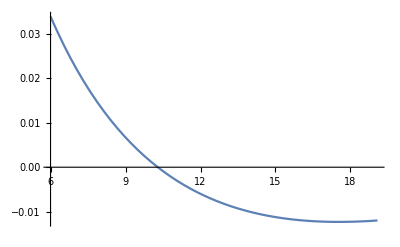

```mathematica
Plot[((λ1SM[t]/.sSM)/.t->{Log[10]*a})[[1]],{a,6,Log[mPl]/Log[10]},PlotRange->All]
```

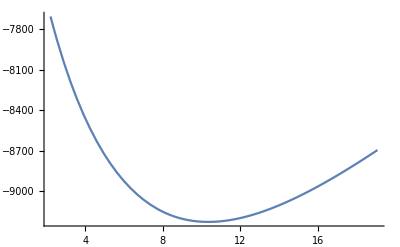

```mathematica
Plot[(μ2SM[t]/.sSM)[[1]]/.t->{Log[10]*a},{a,Log[mtMS]/Log[10],Log[mPl]/Log[10]}]
```

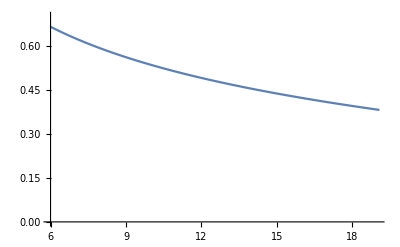

```mathematica
Plot[Sqrt[4*Pi*(αtSM[t]/.sSM)][[1]]/.t->{Log[10]*a},{a,6,Log[mPl]/Log[10]},PlotRange->{{6,19},{0,0.7}}]
```

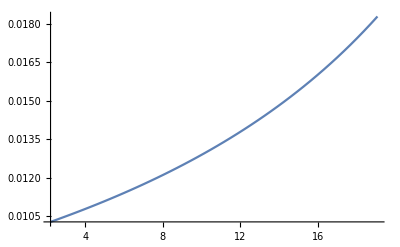

```mathematica
Plot[(α1SM[t]/.sSM)[[1]]/.t->{Log[10]*a},{a,Log[mtMS]/Log[10],Log[mPl]/Log[10]}]
```

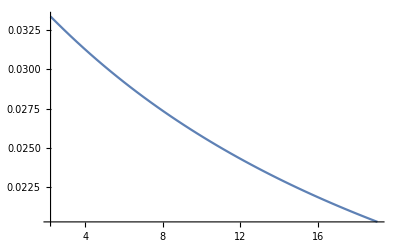

```mathematica
Plot[(α2SM[t]/.sSM)[[1]]/.t->{Log[10]*a},{a,Log[mtMS]/Log[10],Log[mPl]/Log[10]}]
```

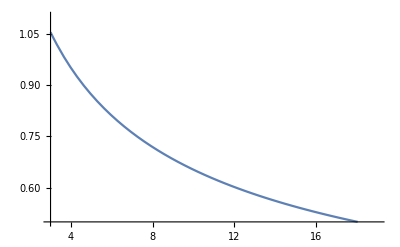

```mathematica
Plot[Sqrt[(α3SM[t]/.sSM)*4*Pi][[1]]/.t->{Log[10]*a},{a,3,Log[mPl]/Log[10]},PlotRange->{{3,19},{0.5,1.1}}]
```

We now compute the effective potential, where our choice of scale is such that

```mathematica
n={6,3,-12,1,3};
κ={1/4g2^2,1/4(g1^2+g2^2),1/2yt^2,3λ1,λ1};
κp={0,0,0,m2,m2};
c={5/6,5/6,3/2,3/2,3/2};
m2i=κ*ϕ^2-κp;
vcontSM=n/(64*Pi^2)*m2i^2*(Log[m2i/μ^2]-c)/.{m2->-2μ2,μ->ϕ}/.replacementListSM;
vefftreeSM=(((μ2SM[t]ϕ^2+1/2λ1SM[t]ϕ^4)/.ϕ->Exp[t])/.sSM)[[1]];
veffSM=vefftreeSM+Simplify[(((Sum[vcontSM[[i]],{i,1,5}])/.ϕ->Exp[t])/.sSM)[[1]]];
```

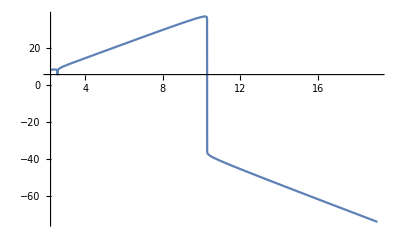

```mathematica
Show[{Plot[(Log10[Abs[Re[vefftreeSM]]+0.])/.t->(x*Log[10]) ,{x,(Log[mtMS])/Log[10],Log[TeV]/Log[10]},PlotRange->All],
Plot[(Sign[Re[vefftreeSM]]*Log10[Abs[Re[vefftreeSM]]+0.])/.t->(x*Log[10]) ,{x,Log[TeV]/Log[10],Log[mPl]/Log[10]},PlotRange->All]}]
```

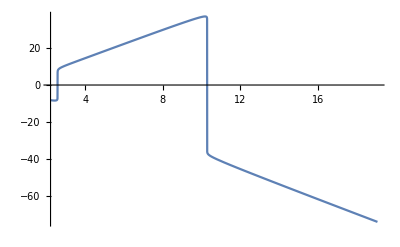

```mathematica
Plot[(Sign[Re[vefftreeSM]]*Log10[Abs[Re[vefftreeSM]]+0.])/.t->(x*Log[10]) ,{x,Log[mtMS]/Log[10],Log[mPl]/Log[10]},PlotRange->All]
```

```mathematica
α1SM'[t]==-(17 α1SM[t] αtSM[t])/(24 π)+(1187 α1SM[t]^2 αtSM[t])/(1728 π^2)-(9 α2SM[t] αtSM[t])/(8 π)-(3 α1SM[t] α2SM[t] αtSM[t])/(32 π^2)-(23 α2SM[t]^2 αtSM[t])/(32 π^2)-(4 α3SM[t] αtSM[t])/π+(19 α1SM[t] α3SM[t] αtSM[t])/(72 π^2)+(9 α2SM[t] α3SM[t] αtSM[t])/(8 π^2)-(27 α3SM[t]^2 αtSM[t])/(2 π^2)+(9 αtSM[t]^2)/(4 π)+(131 α1SM[t] αtSM[t]^2)/(128 π^2)+(225 α2SM[t] αtSM[t]^2)/(128 π^2)+(9 α3SM[t] αtSM[t]^2)/(2 π^2)-(3 αtSM[t]^3)/(2 π^2)-(3 αtSM[t]^2 λ1SM[t])/(8 π^3)+(3 αtSM[t] λ1SM[t]^2)/(64 π^4)/.{α1SM[t]->y[0],α2SM[t]->y[1],α3SM[t]->y[2],λ1SM[t]->y[3],μ2SM[t]->y[4],αtSM[t]->y[5]}
```

α1SM'[t]==-(17 y[0] y[5])/(24 π)+(1187 y[0]^2 y[5])/(1728 π^2)-(9 y[1] y[5])/(8 π)-(3 y[0] y[1] y[5])/(32 π^2)-(23 y[1]^2 y[5])/(32 π^2)-(4 y[2] y[5])/π+(19 y[0] y[2] y[5])/(72 π^2)+(9 y[1] y[2] y[5])/(8 π^2)-(27 y[2]^2 y[5])/(2 π^2)+(3 y[3]^2 y[5])/(64 π^4)+(9 y[5]^2)/(4 π)+(131 y[0] y[5]^2)/(128 π^2)+(225 y[1] y[5]^2)/(128 π^2)+(9 y[2] y[5]^2)/(2 π^2)-(3 y[3] y[5]^2)/(8 π^3)-(3 y[5]^3)/(2 π^2)

```mathematica
{α1SM[Log[mtMS]]==alpha1t,α2SM[Log[mtMS]]==alpha2t,α3SM[Log[mtMS]]==alpha3t,λ1SM[Log[mtMS]]==lambda1mtMS,μ2SM[Log[mtMS]]==-mHphys^2/2,αtSM[Log[mtMS]]==yTopMS^2/(4*Pi)}/.{α1SM->y[0],α2SM->y[1],α3SM->y[2],λ1SM->y[3],μ2SM->y[4],αtSM->y[5]}
```

{y[0][5.09298]==0.0102772,y[1][5.09298]==0.0333685,y[2][5.09298]==0.108301,y[3][5.09298]==0.1271,y[4][5.09298]==-7704.1,y[5][5.09298]==0.069655}

```mathematica
Log[10^10 mPl]
```

66.9573